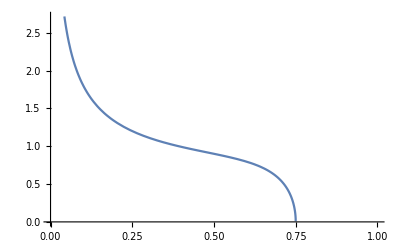

```mathematica
Block[{κ=0.5,λ=0.1,λp,λm},λp=(√(κ(1-λ))+√(λ(1-κ)))^2;λm=(√(κ(1-λ))-√(λ(1-κ)))^2;Plot[(*1/(-(-1+√((-1+λp)/(-1+λm))-λm √((-1+λp)/(-1+λm))+√(λm λp))/(2 λ))**)1/(2π λ)*(√((λp-x)(x-λm)))/(x(1-x)),{x,0,1}]]
```

```mathematica
Block[{κ=0.5,λ=1/4,λp,λm},λp=(√(κ(1-λ))+√(λ(1-κ)))^2;λm=(√(κ(1-λ))-√(λ(1-κ)))^2;NIntegrate[(-x Log[x]-(1-x) Log[1-x])*1/(2π λ)*(√((λp-x)(x-λm)))/(x(1-x)),{x,λm,λp}]]
```

0.556193

```mathematica
Block[{κ=0.5,λ=1/2,λp,λm},λp=(√(κ(1-λ))+√(λ(1-κ)))^2;λm=(√(κ(1-λ))-√(λ(1-κ)))^2;NIntegrate[(-x Log[x]-(1-x) Log[1-x])*1/(2π λ)*(√((λp-x)(x-λm)))/(x(1-x)),{x,λm,λp}]]
```

0.386294

```mathematica
(Block[{κ=0.5,λ=1/4,λp,λm},λp=(√(κ(1-λ))+√(λ(1-κ)))^2;λm=(√(κ(1-λ))-√(λ(1-κ)))^2;NIntegrate[(-x Log[x]-(1-x) Log[1-x])*1/(2π λ)*(√((λp-x)(x-λm)))/(x(1-x)),{x,λm,λp}]]-Block[{κ=0.5,λ=1/2,λp,λm},λp=(√(κ(1-λ))+√(λ(1-κ)))^2;λm=(√(κ(1-λ))-√(λ(1-κ)))^2;NIntegrate[(-x Log[x]-(1-x) Log[1-x])*1/(2π λ)*(√((λp-x)(x-λm)))/(x(1-x)),{x,λm,λp}]])/2
```

0.0849495

```mathematica
k0p5=Table[{λ0,λ0*Block[{κ=0.5,λ=λ0,λp,λm},λp=(√(κ(1-λ))+√(λ(1-κ)))^2;λm=(√(κ(1-λ))-√(λ(1-κ)))^2;NIntegrate[(-x Log[x]-(1-x) Log[1-x])*(*1/(-(-1+√((-1+λp)/(-1+λm))-λm √((-1+λp)/(-1+λm))+√(λm λp))/(2 λ))**)1/(2π λ)*(√((λp-x)(x-λm)))/(x(1-x)),{x,λm,λp}]]},{λ0,0.001,0.5,0.01}];
```

```mathematica
k0p3=Table[{λ0,λ0*Block[{κ=0.3,λ=λ0,λp,λm},λp=(√(κ(1-λ))+√(λ(1-κ)))^2;λm=(√(κ(1-λ))-√(λ(1-κ)))^2;(*1/(-(-1+√((-1+λp)/(-1+λm))-λm √((-1+λp)/(-1+λm))+√(λm λp))/(2 λ))*)NIntegrate[(*1/(-(-1+√((-1+λp)/(-1+λm))-λm √((-1+λp)/(-1+λm))+√(λm λp))/(2 λ))*)(-x Log[x]-(1-x) Log[1-x])*1/(2π λ)*(√((λp-x)(x-λm)))/(x(1-x)),{x,λm,λp}]]},{λ0,0.001,0.5,0.01}];
```

```mathematica
k0p8=Table[{λ0,λ0*Block[{κ=0.8,λ=λ0,λp,λm},λp=(√(κ(1-λ))+√(λ(1-κ)))^2;λm=(√(κ(1-λ))-√(λ(1-κ)))^2;NIntegrate[(-x Log[x]-(1-x) Log[1-x])*(*1/(-(-1+√((-1+λp)/(-1+λm))-λm √((-1+λp)/(-1+λm))+√(λm λp))/(2 λ))**)1/(2π λ)*(√((λp-x)(x-λm)))/(x(1-x)),{x,λm,λp}]]},{λ0,0.001,0.5,0.01}];
```

```mathematica
k0p1=Table[{λ0,λ0*Block[{κ=0.1,λ=λ0,λp,λm},λp=(√(κ(1-λ))+√(λ(1-κ)))^2;λm=(√(κ(1-λ))-√(λ(1-κ)))^2;NIntegrate[(-x Log[x]-(1-x) Log[1-x])(**1/(-(-1+√((-1+λp)/(-1+λm))-λm √((-1+λp)/(-1+λm))+√(λm λp))/(2 λ))*)*1/(2π λ)*(√((λp-x)(x-λm)))/(x(1-x)),{x,λm,λp}]]},{λ0,0.001,0.5,0.01}];
```

```mathematica
k0p=Table[{λ0,(*λ0**)Block[{κ=1-0.8,λ=1-λ0,λp,λm},λp=(√(κ(1-λ))+√(λ(1-κ)))^2;λm=(√(κ(1-λ))-√(λ(1-κ)))^2;λ0*NIntegrate[(-x Log[x]-(1-x) Log[1-x])*1/(-(-1+√((-1+λp)/(-1+λm))-λm √((-1+λp)/(-1+λm))+√(λm λp))/(2 λ))*1/(2π λ)*(√((λp-x)(x-λm)))/(x(1-x)),{x,λm,λp}]]},{λ0,0.001,.5,0.01}];
```

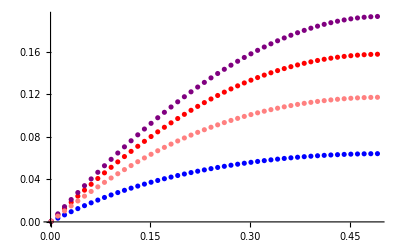

```mathematica
ListPlot[{k0p1,k0p3,k0p5,k0p8},PlotStyle->{Blue,Red,Purple,Pink}]
```

```mathematica
norm=Table[{λ0,Block[{κ=0.3,λ=λ0,λp,λm},λp=(√(κ(1-λ))+√(λ(1-κ)))^2;λm=(√(κ(1-λ))-√(λ(1-κ)))^2;1/(-(-1+√((-1+λp)/(-1+λm))-λm √((-1+λp)/(-1+λm))+√(λm λp))/(2 λ))]},{λ0,0.001,0.5,0.01}]
```

{{0.001,1.},{0.011,1.},{0.021,1.},{0.031,1.},{0.041,1.},{0.051,1.},{0.061,1.},{0.071,1.},{0.081,1.},{0.091,1.},{0.101,1.},{0.111,1.},{0.121,1.},{0.131,1.},{0.141,1.},{0.151,1.},{0.161,1.},{0.171,1.},{0.181,1.},{0.191,1.},{0.201,1.},{0.211,1.},{0.221,1.},{0.231,1.},{0.241,1.},{0.251,1.},{0.261,1.},{0.271,1.},{0.281,1.},{0.291,1.},{0.301,1.00333},{0.311,1.03667},{0.321,1.07},{0.331,1.10333},{0.341,1.13667},{0.351,1.17},{0.361,1.20333},{0.371,1.23667},{0.381,1.27},{0.391,1.30333},{0.401,1.33667},{0.411,1.37},{0.421,1.40333},{0.431,1.43667},{0.441,1.47},{0.451,1.50333},{0.461,1.53667},{0.471,1.57},{0.481,1.60333},{0.491,1.63667}}

```mathematica
normdelta=Table[{λ0,Block[{κ=0.3,λ=λ0,λp,λm},λp=(√(κ(1-λ))+√(λ(1-κ)))^2;λm=(√(κ(1-λ))-√(λ(1-κ)))^2;λ/κ]},{λ0,.3,0.5,0.01}]
```

{{0.3,1.},{0.31,1.03333},{0.32,1.06667},{0.33,1.1},{0.34,1.13333},{0.35,1.16667},{0.36,1.2},{0.37,1.23333},{0.38,1.26667},{0.39,1.3},{0.4,1.33333},{0.41,1.36667},{0.42,1.4},{0.43,1.43333},{0.44,1.46667},{0.45,1.5},{0.46,1.53333},{0.47,1.56667},{0.48,1.6},{0.49,1.63333},{0.5,1.66667}}

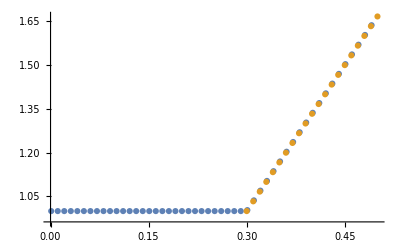

```mathematica
ListPlot[{norm,normdelta}]
```

```mathematica
Block[{κ=0.5,λ=λ0,λp,λm},λp=(√(κ(1-λ))+√(λ(1-κ)))^2;λm=(√(κ(1-λ))-√(λ(1-κ)))^2;NIntegrate[(-x Log[x]-(1-x) Log[1-x])*1/(2π λ)*(√((λp-x)(x-λm)))/(x(1-x)),{x,λm,λp}]]
```

```mathematica
Block[{κ=0.8,λ=.4,λp,λm},λp=(√(κ(1-λ))+√(λ(1-κ)))^2;λm=(√(κ(1-λ))-√(λ(1-κ)))^2;Print[{λp,λm}];NIntegrate[(-x Log[x]-(1-x) Log[1-x])*1/(-(-1+√((-1+λp)/(-1+λm))-λm √((-1+λp)/(-1+λm))+√(λm λp))/(2 λ))*1/(2π λ)*(√((λp-x)(x-λm)))/(x(1-x)),{x,λm,λp}]]
```

{0.951918,0.168082}

0.565586

```mathematica
Log[2]
```

Log[2]

```mathematica
Integrate[1/(2π λ)*(√((λp-x)(x-λm)))/(x(1-x)),{x,λm,λp},Assumptions->{λp<1,λm<1,λp>0,λm>0,λm<λp}]
```

-(-1+√((-1+λp)/(-1+λm))-λm √((-1+λp)/(-1+λm))+√(λm λp))/(2 λ)